```mathematica
param2=Import["C:\\Users\\s4baan\\Documents\\Advise\\Definition Files\\TestEqCorr\\Param_US2.csv"];
```

```mathematica
param2=Import["C:\\Users\\s4baan\\Documents\\Advise\\Definition Files\\TestEqCorr\\Param_US3.csv"];
```

```mathematica
parUS2={θa1->param2[[17,2]]+param2[[17,5]],ka1->param2[[17,3]]-param2[[17,6]],σa1->param2[[17,4]],x01->param2[[17,9]],
θa2->param2[[18,2]]+param2[[18,5]],ka2->param2[[18,3]]-param2[[18,6]],σa2->param2[[18,4]] ,x02-> param2[[18,9]],θa3->param2[[19,2]]+param2[[19,5]],ka3->param2[[19,3]]-param2[[19,6]],σa3->param2[[19,4]] ,x03-> param2[[19,9]],l0->param2[[24,2]] ,
v0a-> param2[[81,2]], αa-> param2[[82,2]],βa-> param2[[84,2]],σa-> param2[[86,2]],v0b-> param2[[121,2]], αb-> param2[[122,2]],βb-> param2[[124,2]],σb-> param2[[126,2]],ρbb12-> param2[[153,9]],ρaa12->param2[[150,6]] ,ρab11->param2[[151,6]],ρab12-> param2[[153,6]],ρba12-> param2[[151,8]],ρab22-> param2[[153,8]],μ0a-> param2[[67,2]],μ1a-> param2[[68,2]],μa0-> param2[[67,2]],μa1-> param2[[68,2]]-1/2-param2[[70,2]]*(Exp[param2[[73,2]]+param2[[75,2]]^2/2]-1),μ0b->param2[[107,2]],μ1b->param2[[108,2]],μb0->param2[[107,2]],μb1->param2[[108,2]]-1/2-param2[[110,2]]*(Exp[param2[[113,2]]+param2[[115,2]]^2/2]-1),λ0a-> param2[[69,2]],λ0b->param2[[109,2]],λ1a->param2[[70,2]] ,λ1b->param2[[110,2]],mνa->param2[[73,2]],σνa->param2[[75,2]],mνb->param2[[113,2]],σνb->param2[[115,2]] ,sa0-> Log[param2[[165,1]]],sb0->Log[param2[[165,2]]]};
parExtra={ξa-> 0,ξb-> 0,ua-> 1.0,ub-> 1.0,wa1-> 1.0,wa2-> 1.0,wa3-> 1.0,ψa-> 1.0,ψb-> 1.0,ta-> 30.0};
```

```mathematica
parExtra={ξa-> 0,ξb-> 0,ua-> 0.6,ub-> 0.8,wa1-> 1.2,wa2-> 3.5,wa3-> 2.7,ψa-> 0.8,ψb-> 0.67,ta-> 30.0};
```

```mathematica
muva[t_]:=ⅇ^(- βa*t)(v0a-αa/βa)+αa/βa
```

```mathematica
varva[t_]:=σa^2/βa(αa/(2 βa)+ⅇ^(-t βa)(v0a-αa/βa)-ⅇ^(-2 t βa)(v0a-αa/(2 βa)))
```

```mathematica
muvb[t_]:=ⅇ^(- βb*t)(v0b-αb/βb)+αb/βb
```

```mathematica
varvb[t_]:=σb^2/βb(αb/(2 βb)+ⅇ^(-t βb)(v0b-αb/βb)-ⅇ^(-2 t βb)(v0b-αb/(2 βb)))
```

```mathematica
Θ2[t_]:=(√muva[t])(√muvb[t])
```

```mathematica
(* Θ[t_]:=(√muVx[t]-(5VarVx[t])/(4(√muVx[t])^3))(√muVy[t]-(5VarVy[t])/(4(√muVy[t])^3)) *)
```

```mathematica
solvar2N=NDSolve[{Bx1'[t]==1/2(Bx1[t]σa1)^2-ka1*Bx1[t]+ua+ub,Bx2'[t]==1/2(Bx2[t]σa2)^2-ka2*Bx2[t]+ua+ub,Bx3'[t]==1/2(Bx3[t]σa3)^2-ka3*Bx3[t]+ua+ub,Ca'[t]==1/2(Ca[t]σa)^2-Ca[t](βa-ua*σa*ρaa12)+1/2 ua^2+ua*(μ1a-1/2)+λ1a*((ⅇ^(ξa+ua*mνa+(ua*σνa)^2/2)-1)-ua*(ⅇ^(mνa+σνa^2/2)-1)),Cb'[t]==1/2(Cb[t]σb)^2-Cb[t](βb-ub*σb*ρbb12)+1/2 ub^2+ub*(μ1b-1/2)+λ1b*((ⅇ^(ξb+ub*mνb+(ub*σνb)^2/2)-1)-ub*(ⅇ^(mνb+σνb^2/2)-1)),
AA'[t]==θa1*Bx1[t]+θa2*Bx2[t]+θa3*Bx3[t]+αa*Ca[t]+αb*Cb[t]+ua*l0+ub*l0+ua*μ0a+ub*μ0b+λ0a*(ⅇ^(ξa+ua*mνa+(ua*σva)^2/2)-1)+λ0b*(ⅇ^(ξb+ub*mνb+(ub*σvb)^2/2)-1)+Θ2[30.0]*(ua*ub*ρab11+ua*ρab12*Cb[t]+ub*ρba12*Ca[t]),Bx1[0]==wa1,Bx2[0]==wa2,Bx3[0]==wa3,Ca[0]==ψa,Cb[0]==ψb,AA[0]==0}/.parUS2/.parExtra,{Bx1[t],Bx2[t],Bx3[t],Ca[t],Cb[t],AA[t]},{t,0.0,30.}];
```

```mathematica
γxa1[ua_,ub_]:=√(ka1^2-2 (ua+ub) σa1^2)
```

```mathematica
Bxa1[ua_,ub_,wa1_,τ_]:=((ⅇ^(γxa1[ua,ub] τ)-1)(2(ua+ub)+wa1(-ka1+γxa1[ua,ub]))+2wa1 γxa1[ua,ub])/((ⅇ^(γxa1[ua,ub] τ)-1)(ka1+γxa1[ua,ub]-(σa1)^2 wa1)+2γxa1[ua,ub])
```

```mathematica
Bxaint1[ua_,ub_,wa1_,τ_]:=1/σa1^2((ka1+γxa1[ua,ub])*τ+2Log[(2γxa1[ua,ub])/((ⅇ^(γxa1[ua,ub] τ)-1)(ka1+γxa1[ua,ub]-(σa1)^2 wa1)+2γxa1[ua,ub])])
```

```mathematica
γxa2[ua_,ub_]:=√(ka2^2-2 (ua+ub) σa2^2)
```

```mathematica
Bxa2[ua_,ub_,wa2_,τ_]:=((ⅇ^(γxa2[ua,ub] τ)-1)(2(ua+ub)+wa2(-ka2+γxa2[ua,ub]))+2wa2 γxa2[ua,ub])/((ⅇ^(γxa2[ua,ub] τ)-1)(ka2+γxa2[ua,ub]-(σa2)^2 wa2)+2γxa2[ua,ub])
```

```mathematica
Bxaint2[ua_,ub_,wa2_,τ_]:=1/σa2^2((ka2+γxa2[ua,ub])*τ+2Log[(2γxa2[ua,ub])/((ⅇ^(γxa2[ua,ub] τ)-1)(ka2+γxa2[ua,ub]-(σa2)^2 wa2)+2γxa2[ua,ub])])
```

```mathematica
γxa3[ua_,ub_]:=√(ka3^2-2 (ua+ub) σa3^2)
```

```mathematica
Bxa3[ua_,ub_,wa3_,τ_]:=((ⅇ^(γxa3[ua,ub] τ)-1)(2(ua+ub)+wa3(-ka3+γxa3[ua,ub]))+2wa3 γxa3[ua,ub])/((ⅇ^(γxa3[ua,ub] τ)-1)(ka3+γxa3[ua,ub]-(σa3)^2 wa3)+2γxa3[ua,ub])
```

```mathematica
Bxaint3[ua_,ub_,wa3_,τ_]:=1/σa3^2((ka3+γxa3[ua,ub])*τ+2Log[(2γxa3[ua,ub])/((ⅇ^(γxa3[ua,ub] τ)-1)(ka3+γxa3[ua,ub]-(σa3)^2 wa3)+2γxa3[ua,ub])])
```

```mathematica
γva[ua_]:=√((ua*σa*ρaa12-βa)^2-2 σa^2(1/2 ua^2+ua*(μ1a-1/2)+λ1a*((ⅇ^(ξa+ua*mνa+(ua*σνa)^2/2)-1)-ua*(ⅇ^(mνa+σνa^2/2)-1))))
```

```mathematica
Bva[ua_,ψa_,τ_]:=((ⅇ^(γva[ua] τ)-1)(ψa(γva[ua]-βa+ua*σa*ρaa12)+(ua^2+ua*(2*μ1a-1)+2*λ1a*((ⅇ^(ξa+ua*mνa+(ua*σνa)^2/2)-1)-ua*(ⅇ^(mνa+σνa^2/2)-1))))+2ψa*γva[ua])/((ⅇ^(γva[ua] τ)-1)(βa-ua*σa*ρaa12+γva[ua]-σa^2 ψa)+2γva[ua])
```

```mathematica
Bvaint[ua_,ψa_,τ_]:=1/σa^2((βa-ua*σa*ρaa12+γva[ua])*τ+2Log[(2γva[ua])/((ⅇ^(γva[ua] τ)-1)(βa-ua*σa*ρaa12+γva[ua]-σa^2 ψa)+2γva[ua])])
```

```mathematica
γvb[ub_]:=√((ub*σb*ρbb12-βb)^2-2 σb^2(1/2 ub^2+ub*(μ1b-1/2)+λ1b*((ⅇ^(ξb+ub*mνb+(ub*σνb)^2/2)-1)-ub*(ⅇ^(mνb+σνb^2/2)-1))))
```

```mathematica
Bvb[ub_,ψb_,τ_]:=((ⅇ^(γvb[ub] τ)-1)(ψb(γvb[ub]-βb+ub*σb*ρbb12)+(ub^2+ub*(2*μ1b-1)+2*λ1b*((ⅇ^(ξb+ub*mνb+(ub*σνb)^2/2)-1)-ub*(ⅇ^(mνb+σνb^2/2)-1))))+2ψb*γvb[ub])/((ⅇ^(γvb[ub] τ)-1)(βb-ub*σb*ρbb12+γvb[ub]-σb^2 ψb)+2γvb[ub])
```

```mathematica
Bvbint[ub_,ψb_,τ_]:=1/σb^2((βb-ub*σb*ρbb12+γvb[ub])*τ+2Log[(2γvb[ub])/((ⅇ^(γvb[ub] τ)-1)(βb-ub*σb*ρbb12+γvb[ub]-σb^2 ψb)+2γvb[ub])])
```

```mathematica
A[ua_,ub_,ψa_,ψb_,wa1_,wa2_,wa3_,τ_,t_]:=θa1*Bxaint1[ua,ub,wa1,τ]+θa2*Bxaint2[ua,ub,wa2,τ]+θa3*Bxaint3[ua,ub,wa3,τ]+αa*Bvaint[ua,ψa,τ]+αb*Bvbint[ub,ψb,τ]+ua*(l0+μa0)*τ+ub*(l0+μb0)*τ+(ⅇ^(ξa+ua*mνa+(ua*σνa)^2/2)-1)*λ0a*τ+(ⅇ^(ξb+ua*mνb+(ua*σνb)^2/2)-1)*λ0b*τ+Θ2[30.0]*(ua*ub*ρab11*τ+ua*ρab12*Bvbint[ub,ψb,τ]+ub*ρba12*Bvaint[ua,ψa,τ])
```

```mathematica
Bxn1=Array[uu,31];Bxn2=Array[uu,31];Bxn3=Array[uu,31];Can=Array[uu,31];Cbn=Array[uu,31];AAn=Array[uu,31];
```

```mathematica
Bx1e=Array[uu,31];Bx2e=Array[uu,31];Bx3e=Array[uu,31];Cae=Array[uu,31];Cbe=Array[uu,31];AAe=Array[uu,31];
```

```mathematica
ti=1;i=0;Do[Bxn1[[i+1]]=Evaluate[Bx1[t]/.solvar2N]/.t-> ti;Bxn2[[i+1]]=Evaluate[Bx2[t]/.solvar2N]/.t-> ti;Bxn3[[i+1]]=Evaluate[Bx3[t]/.solvar2N]/.t-> ti;Can[[i+1]]=Evaluate[Ca[t]/.solvar2N]/.t-> ti;Cbn[[i+1]]=Evaluate[Cb[t]/.solvar2N]/.t-> ti;AAn[[i+1]]=Evaluate[AA[t]/.solvar2N]/.t-> ti;
Bx1e[[i+1]]=Bxa1[ua,ub,wa1,t]/.parUS2/.parExtra/.t-> ti;Bx2e[[i+1]]=Bxa2[ua,ub,wa2,t]/.parUS2/.parExtra/.t-> ti;Bx3e[[i+1]]=Bxa3[ua,ub,wa3,t]/.parUS2/.parExtra/.t-> ti;
Cae[[i+1]]=Bva[ua,ψa,t]/.parUS2/.parExtra/.t-> ti;Cbe[[i+1]]=Bvb[ub,ψb,t]/.parUS2/.parExtra/.t-> ti;
AAe[[i+1]]=A[ua,ub,ψa,ψb,wa1,wa2,wa3,t,30.0]/.parUS2/.parExtra/.t-> ti;
ti=ti+1,{i,1,30}]
```

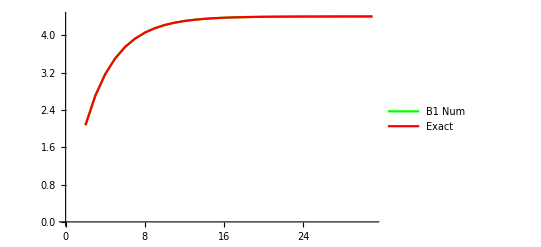
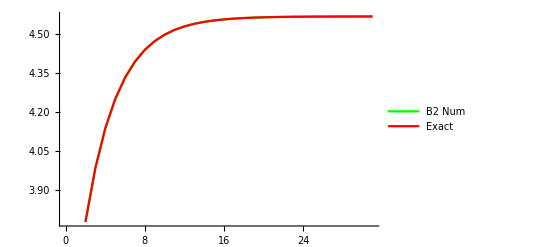
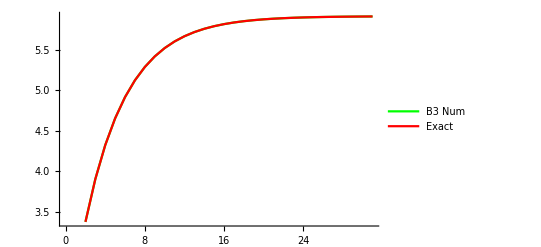
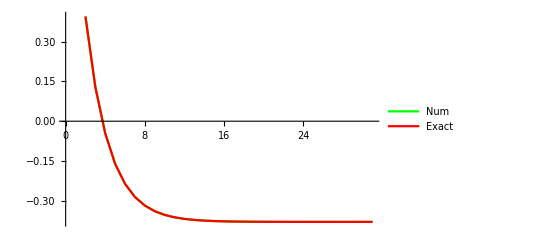
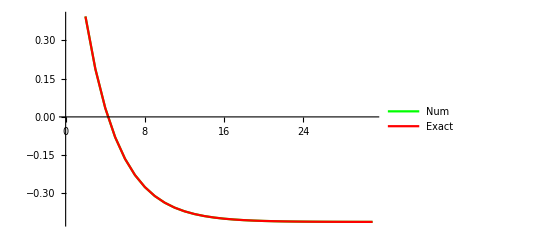
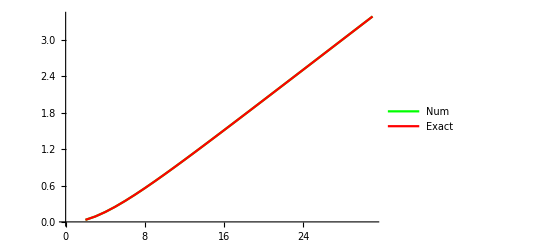

```mathematica
{ListLinePlot[{Flatten[Bxn1],Bx1e},PlotRange->All,PlotLegends->{"B1 Num","Exact"},PlotStyle-> {Green,Red}],ListLinePlot[{Flatten[Bxn2],Bx2e},PlotRange->All,PlotLegends->{"B2 Num","Exact"},PlotStyle-> {Green,Red}],ListLinePlot[{Flatten[Bxn3],Bx3e},PlotRange->All,PlotLegends->{"B3 Num","Exact"},PlotStyle-> {Green,Red}],
ListLinePlot[{Flatten[Can],Cae},PlotRange->All,PlotLegends->{"Num","Exact"},PlotStyle-> {Green,Red}],ListLinePlot[{Flatten[Cbn],Cbe},PlotRange->All,PlotLegends->{"Num","Exact"},PlotStyle-> {Green,Red}],ListLinePlot[{Flatten[AAn],AAe},PlotRange->All,PlotLegends->{"Num","Exact"},PlotStyle-> {Green,Red}]}
```

```mathematica
(*+Θ2[t]*(ua*ub*ρab11+ua*ρab12*Bvbint[ub,ψb,τ]+ub*ρba12*Bvaint[ua,ψa,τ])*τ*)
```

```mathematica
ϕ[ua_,ub_,ξa_,ξb_,ψa_,ψb_,wa1_,wa2_,wa3_,τ_,t_]:=Exp[A[ua,ub,ψa,ψb,wa1,wa2,wa3,τ,t]+Bxa1[ua,ub,wa1,τ]*x01+Bxa2[ua,ub,wa2,τ]*x02+Bxa3[ua,ub,wa3,τ]*x03+Bva[ua,ψa,τ]*v0a+Bvb[ub,ψb,τ]*v0b+ua*sa0+ub*sb0+ξa*Na+ξb*Nb]
```

```mathematica
ϕnum[ua_,ub_,ξa_,ξb_,ψa_,ψb_,wa1_,wa2_,wa3_,τ_,t_]=ϕ[ua,ub,ξa,ξb,ψa,ψb,wa1,wa2,wa3,τ,t]/.parUS2;
```

```mathematica
ϕc[ua_,ub_,h_,τ_,t_]:=Exp[A[ua,ub,0,0,0,0,0,τ,t]+A[0,0,Bva[ua,0,τ],Bvb[ub,0,τ],Bxa1[ua,ub,0,τ],Bxa2[ua,ub,0,τ],Bxa3[ua,ub,0,τ],h,t]+Bxa1[0,0,Bxa1[ua,ub,0,τ],h]*x01+Bxa2[0,0,Bxa2[ua,ub,0,τ],h]*x02+Bxa3[0,0,Bxa3[ua,ub,0,τ],h]*x03+Bva[0,Bva[ua,0,τ],h]*v0a+Bvb[0,Bvb[ub,0,τ],h]*v0b]
```

```mathematica
MeanA=D[ϕc[ua,ub,h,τ,t],{ua}]/.{ua-> 0,ub-> 0,ξa-> 0,ξb-> 0}/.parUS2/.{h-> 30.0,τ-> 1}
```

0.0694734

```mathematica
VarA=(D[ϕc[ua,ub,h,τ,t],{ua,2}]/.{ua-> 0,ub-> 0,ξa-> 0,ξb-> 0}/.parUS2/.{h-> 30.0,τ-> 1})-MeanA^2
```

0.0266481

```mathematica
Sqrt[VarA]
```

0.163242

```mathematica
MeanB=D[ϕc[ua,ub,h,τ,t],{ub}]/.{ua-> 0,ub-> 0,ξa-> 0,ξb-> 0}/.parUS2/.{h-> 30.0,τ-> 1}
```

0.0694488

```mathematica
VarB=(D[ϕc[ua,ub,h,τ,t],{ub,2}]/.{ua-> 0,ub-> 0,ξa-> 0,ξb-> 0}/.parUS2/.{h-> 30.0,τ-> 1})-MeanB^2
```

0.0292187

```mathematica
Sqrt[VarB]
```

0.170935

```mathematica
CovAB=(D[D[ϕc[ua,ub,h,τ,t],{ua}],{ub}]/.{ua-> 0,ub-> 0,ξa-> 0,ξb-> 0}/.parUS2/.{h-> 30.0,τ-> 1})-MeanA*MeanB
```

0.0213355

```mathematica
CorrAB=CovAB/(Sqrt[VarA]*Sqrt[VarB])
```

0.764609

```mathematica
Simplify[(D[D[ϕc[ua,ub,h,τ,t],{ua}],{ub}]/.{ua-> 0,ub-> 0,ξa-> 0,ξb-> 0})-(D[ϕc[ua,ub,h,τ,t],{ua}]/.{ua-> 0,ub-> 0,ξa-> 0,ξb-> 0})*(D[ϕc[ua,ub,h,τ,t],{ub}]/.{ua-> 0,ub-> 0,ξa-> 0,ξb-> 0}),Assumptions->  {ka1>0,ka2>0,ka3>0,ka1*τ>0,ka2*τ>0,ka3*τ>0,βa>0,βb>0}]
```

Simplify::time: Time spent on a transformation exceeded 300. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify :: time will be suppressed during this calculation.

$Aborted

```mathematica
Exp[A[ua,ub,0,0,0,0,0,τ,t]+A[0,0,Bva[ua,0,τ],Bvb[ub,0,τ],Bxa1[ua,ub,0,τ],Bxa2[ua,ub,0,τ],Bxa3[ua,ub,0,τ],h,t]+Bxa1[0,0,Bxa1[ua,ub,0,τ],h]*x01+Bxa2[0,0,Bxa2[ua,ub,0,τ],h]*x02+Bxa3[0,0,Bxa3[ua,ub,0,τ],h]*x03+Bva[0,Bva[ua,0,τ],h]*v0a+Bvb[0,Bvb[ub,0,τ],h]*v0b]
```

```mathematica
Simplify[(Exp[A[ua,ub,0,0,0,0,0,τ,t]+A[0,0,Bva[ua,0,τ],Bvb[ub,0,τ],Bxa1[ua,ub,0,τ],Bxa2[ua,ub,0,τ],Bxa3[ua,ub,0,τ],h,t]+Bxa1[0,0,Bxa1[ua,ub,0,τ],h]*x01+Bxa2[0,0,Bxa2[ua,ub,0,τ],h]*x02+Bxa3[0,0,Bxa3[ua,ub,0,τ],h]*x03+Bva[0,Bva[ua,0,τ],h]*v0a+Bvb[0,Bvb[ub,0,τ],h]*v0b]/.{ua-> 0,ub-> 0,ξa-> 0,ξb-> 0}),Assumptions->  {ka1>0,ka2>0,ka3>0,ka1*τ>0,ka2*τ>0,ka3*τ>0,βa>0,βb>0,h*βa>0,h*βb>0}]
```

1

```mathematica
Simplify[(D[D[A[ua,ub,0,0,0,0,0,τ,t],{ua}],{ub}]/.{ua-> 0,ub-> 0,ξa-> 0,ξb-> 0}),Assumptions->  {ka1>0,ka2>0,ka3>0,ka1*τ>0,ka2*τ>0,ka3*τ>0,βa>0,βb>0}]
```

Simplify::time: Time spent on a transformation exceeded 300. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

(ⅇ^(-2 ka1 τ) θa1 σa1^2 (1+4 ⅇ^(ka1 τ) (1+ka1 τ)+ⅇ^(2 ka1 τ) (-5+2 ka1 τ)))/(2 ka1^4)+(ⅇ^(-2 ka2 τ) θa2 σa2^2 (1+4 ⅇ^(ka2 τ) (1+ka2 τ)+ⅇ^(2 ka2 τ) (-5+2 ka2 τ)))/(2 ka2^4)+(ⅇ^(-2 ka3 τ) θa3 σa3^2 (1+4 ⅇ^(ka3 τ) (1+ka3 τ)+ⅇ^(2 ka3 τ) (-5+2 ka3 τ)))/(2 ka3^4)+√(ⅇ^(-30. βa) (v0a-αa/βa)+αa/βa) √(ⅇ^(-30. βb) (v0b-αb/βb)+αb/βb) (ρab11 τ-(ⅇ^(-βa τ) (1+2 (-1+ⅇ^(mνa+σνa^2/2)-mνa) λ1a-2 μ1a) ρba12 (1+ⅇ^(βa τ) (-1+βa τ)))/(2 βa^2)-(ⅇ^(-βb τ) (1+2 (-1+ⅇ^(mνb+σνb^2/2)-mνb) λ1b-2 μ1b) ρab12 (1+ⅇ^(βb τ) (-1+βb τ)))/(2 βb^2))

```mathematica
Simplify[(D[D[Bxa1[0,0,Bxa1[ua,ub,0,τ],h],{ua}],{ub}]/.{ua-> 0,ub-> 0,ξa-> 0,ξb-> 0}),Assumptions->  {ka1>0,ka2>0,ka3>0,ka1*τ>0,ka2*τ>0,ka3*τ>0,βa>0,βb>0}]
```

-(ⅇ^(-2 ka1 (h+τ)) σa1^2 (1-2 ⅇ^(ka1 τ)+ⅇ^(2 ka1 τ)-2 ⅇ^(ka1 (h+2 τ))+2 ⅇ^(ka1 (h+τ)) (1+ka1 τ)))/ka1^3

```mathematica
Simplify[(D[D[Bxa2[0,0,Bxa2[ua,ub,0,τ],h],{ua}],{ub}]/.{ua-> 0,ub-> 0,ξa-> 0,ξb-> 0}),Assumptions->  {ka1>0,ka2>0,ka3>0,ka1*τ>0,ka2*τ>0,ka3*τ>0,βa>0,βb>0}]
```

-(ⅇ^(-2 ka2 (h+τ)) σa2^2 (1-2 ⅇ^(ka2 τ)+ⅇ^(2 ka2 τ)-2 ⅇ^(ka2 (h+2 τ))+2 ⅇ^(ka2 (h+τ)) (1+ka2 τ)))/ka2^3

```mathematica
Simplify[(D[D[Bxa3[0,0,Bxa3[ua,ub,0,τ],h],{ua}],{ub}]/.{ua-> 0,ub-> 0,ξa-> 0,ξb-> 0}),Assumptions->  {ka1>0,ka2>0,ka3>0,ka1*τ>0,ka2*τ>0,ka3*τ>0,βa>0,βb>0}]
```

-(ⅇ^(-2 ka3 (h+τ)) σa3^2 (1-2 ⅇ^(ka3 τ)+ⅇ^(2 ka3 τ)-2 ⅇ^(ka3 (h+2 τ))+2 ⅇ^(ka3 (h+τ)) (1+ka3 τ)))/ka3^3

```mathematica
Simplify[(D[D[Bva[0,Bva[ua,0,τ],h],{ua}],{ub}]/.{ua-> 0,ub-> 0,ξa-> 0,ξb-> 0}),Assumptions->  {ka1>0,ka2>0,ka3>0,ka1*τ>0,ka2*τ>0,ka3*τ>0,βa>0,βb>0}]
```

0

```mathematica
Simplify[(D[D[Bvb[0,Bvb[ub,0,τ],h],{ua}],{ub}]/.{ua-> 0,ub-> 0,ξa-> 0,ξb-> 0}),Assumptions->  {ka1>0,ka2>0,ka3>0,ka1*τ>0,ka2*τ>0,ka3*τ>0,βa>0,βb>0}]
```

0

```mathematica
Simplify[(D[D[A[0,0,Bva[ua,0,τ],Bvb[ub,0,τ],Bxa1[ua,ub,0,τ],Bxa2[ua,ub,0,τ],Bxa3[ua,ub,0,τ],h,t],{ua}],{ub}]/.{ua-> 0,ub-> 0,ξa-> 0,ξb-> 0}),Assumptions->  {ka1>0,ka2>0,ka3>0,ka1*τ>0,ka2*τ>0,ka3*τ>0,βa>0,βb>0}]
```

Simplify::time: Time spent on a transformation exceeded 300. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

1/2 ((ⅇ^(-2 ka1 (h+τ)) (-1+ⅇ^(h ka1))^2 (-1+ⅇ^(ka1 τ))^2 θa1 σa1^2)/ka1^4+(ⅇ^(-2 ka2 (h+τ)) (-1+ⅇ^(h ka2))^2 (-1+ⅇ^(ka2 τ))^2 θa2 σa2^2)/ka2^4+(ⅇ^(-2 ka3 (h+τ)) (-1+ⅇ^(h ka3))^2 (-1+ⅇ^(ka3 τ))^2 θa3 σa3^2)/ka3^4+(2 ⅇ^(-ka1 (h+2 τ)) (-1+ⅇ^(h ka1)) θa1 σa1^2 (-1+ⅇ^(2 ka1 τ)-2 ⅇ^(ka1 τ) ka1 τ))/ka1^4+(2 ⅇ^(-ka2 (h+2 τ)) (-1+ⅇ^(h ka2)) θa2 σa2^2 (-1+ⅇ^(2 ka2 τ)-2 ⅇ^(ka2 τ) ka2 τ))/ka2^4+(2 ⅇ^(-ka3 (h+2 τ)) (-1+ⅇ^(h ka3)) θa3 σa3^2 (-1+ⅇ^(2 ka3 τ)-2 ⅇ^(ka3 τ) ka3 τ))/ka3^4)

```mathematica
Simplify[D[ϕc[ua,ub,h,τ,t],{ua}]/.{ua-> 0,ub-> 0,ξa-> 0,ξb-> 0},Assumptions->  {ka1>0,ka2>0,ka3>0,ka1*τ>0,ka2*τ>0,ka3*τ>0,βa>0,βb>0}]
```

Simplify::time: Time spent on a transformation exceeded 300. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

ⅇ^(2 ((h αa βa)/σa^2+(h ka1 θa1)/σa1^2+(h ka2 θa2)/σa2^2+(h ka3 θa3)/σa3^2+(h αb βb)/σb^2+(θa1 Log[ⅇ^(-h ka1)])/σa1^2+(θa2 Log[ⅇ^(-h ka2)])/σa2^2+(θa3 Log[ⅇ^(-h ka3)])/σa3^2+(αa Log[ⅇ^(-h βa)])/σa^2+(αb Log[ⅇ^(-h βb)])/σb^2)) ((ⅇ^(-ka1 (h+τ)) (-1+ⅇ^(ka1 τ)) x01)/ka1+(ⅇ^(-ka2 (h+τ)) (-1+ⅇ^(ka2 τ)) x02)/ka2+(ⅇ^(-ka3 (h+τ)) (-1+ⅇ^(ka3 τ)) x03)/ka3+(ⅇ^(-ka1 (h+τ)) (-1+ⅇ^(h ka1)) (-1+ⅇ^(ka1 τ)) θa1)/ka1^2+(ⅇ^(-ka2 (h+τ)) (-1+ⅇ^(h ka2)) (-1+ⅇ^(ka2 τ)) θa2)/ka2^2+(ⅇ^(-ka3 (h+τ)) (-1+ⅇ^(h ka3)) (-1+ⅇ^(ka3 τ)) θa3)/ka3^2-(ⅇ^(-βa (h+τ)) (-1+ⅇ^(h βa)) (-1+ⅇ^(βa τ)) αa (1+2 (-1+ⅇ^(mνa+σνa^2/2)-mνa) λ1a-2 μ1a))/(2 βa^2)-(ⅇ^(-βa (h+τ)) (-1+ⅇ^(βa τ)) v0a (1+2 (-1+ⅇ^(mνa+σνa^2/2)-mνa) λ1a-2 μ1a))/(2 βa)+mνa λ0a τ+mνb λ0b τ+(l0+μa0) τ-(θa1 (1-ⅇ^(-ka1 τ)-ka1 τ))/ka1^2-(θa2 (1-ⅇ^(-ka2 τ)-ka2 τ))/ka2^2-(θa3 (1-ⅇ^(-ka3 τ)-ka3 τ))/ka3^2-(ⅇ^(-βa τ) αa (1+2 (-1+ⅇ^(mνa+σνa^2/2)-mνa) λ1a-2 μ1a) (1+ⅇ^(βa τ) (-1+βa τ)))/(2 βa^2))

```mathematica
h ka1>0,h ka2>0,h ka3>0,h *βa>0,h *βb
```

```mathematica
Simplify[D[ϕc[ua,ub,h,τ,t],{ub}]/.{ua-> 0,ub-> 0,ξa-> 0,ξb-> 0},Assumptions->  {ka1>0,ka2>0,ka3>0,ka1*τ>0,ka2*τ>0,ka3*τ>0,βa>0,βb>0}]
```

Simplify::time: Time spent on a transformation exceeded 300. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

ⅇ^(2 ((h αa βa)/σa^2+(h ka1 θa1)/σa1^2+(h ka2 θa2)/σa2^2+(h ka3 θa3)/σa3^2+(h αb βb)/σb^2+(θa1 Log[ⅇ^(-h ka1)])/σa1^2+(θa2 Log[ⅇ^(-h ka2)])/σa2^2+(θa3 Log[ⅇ^(-h ka3)])/σa3^2+(αa Log[ⅇ^(-h βa)])/σa^2+(αb Log[ⅇ^(-h βb)])/σb^2)) ((ⅇ^(-ka1 (h+τ)) (-1+ⅇ^(ka1 τ)) x01)/ka1+(ⅇ^(-ka2 (h+τ)) (-1+ⅇ^(ka2 τ)) x02)/ka2+(ⅇ^(-ka3 (h+τ)) (-1+ⅇ^(ka3 τ)) x03)/ka3+(ⅇ^(-ka1 (h+τ)) (-1+ⅇ^(h ka1)) (-1+ⅇ^(ka1 τ)) θa1)/ka1^2+(ⅇ^(-ka2 (h+τ)) (-1+ⅇ^(h ka2)) (-1+ⅇ^(ka2 τ)) θa2)/ka2^2+(ⅇ^(-ka3 (h+τ)) (-1+ⅇ^(h ka3)) (-1+ⅇ^(ka3 τ)) θa3)/ka3^2-(ⅇ^(-βb (h+τ)) (-1+ⅇ^(h βb)) (-1+ⅇ^(βb τ)) αb (1+2 (-1+ⅇ^(mνb+σνb^2/2)-mνb) λ1b-2 μ1b))/(2 βb^2)-(ⅇ^(-βb (h+τ)) (-1+ⅇ^(βb τ)) v0b (1+2 (-1+ⅇ^(mνb+σνb^2/2)-mνb) λ1b-2 μ1b))/(2 βb)+(l0+μb0) τ-(θa1 (1-ⅇ^(-ka1 τ)-ka1 τ))/ka1^2-(θa2 (1-ⅇ^(-ka2 τ)-ka2 τ))/ka2^2-(θa3 (1-ⅇ^(-ka3 τ)-ka3 τ))/ka3^2-(ⅇ^(-βb τ) αb (1+2 (-1+ⅇ^(mνb+σνb^2/2)-mνb) λ1b-2 μ1b) (1+ⅇ^(βb τ) (-1+βb τ)))/(2 βb^2))

```mathematica
MeanLCA=((ⅇ^(-ka1 (h+τ)) (-1+ⅇ^(ka1 τ)) x01)/ka1+(ⅇ^(-ka2 (h+τ)) (-1+ⅇ^(ka2 τ)) x02)/ka2+(ⅇ^(-ka3 (h+τ)) (-1+ⅇ^(ka3 τ)) x03)/ka3+(ⅇ^(-ka1 (h+τ)) (-1+ⅇ^(h ka1)) (-1+ⅇ^(ka1 τ)) θa1)/ka1^2+(ⅇ^(-ka2 (h+τ)) (-1+ⅇ^(h ka2)) (-1+ⅇ^(ka2 τ)) θa2)/ka2^2+(ⅇ^(-ka3 (h+τ)) (-1+ⅇ^(h ka3)) (-1+ⅇ^(ka3 τ)) θa3)/ka3^2-(ⅇ^(-βa (h+τ)) (-1+ⅇ^(h βa)) (-1+ⅇ^(βa τ)) αa (1+2 (-1+ⅇ^(mνa+σνa^2/2)-mνa) λ1a-2 μ1a))/(2 βa^2)-(ⅇ^(-βa (h+τ)) (-1+ⅇ^(βa τ)) v0a (1+2 (-1+ⅇ^(mνa+σνa^2/2)-mνa) λ1a-2 μ1a))/(2 βa)+mνa λ0a τ+mνb λ0b τ+(l0+μa0) τ-(θa1 (1-ⅇ^(-ka1 τ)-ka1 τ))/ka1^2-(θa2 (1-ⅇ^(-ka2 τ)-ka2 τ))/ka2^2-(θa3 (1-ⅇ^(-ka3 τ)-ka3 τ))/ka3^2-(ⅇ^(-βa τ) αa (1+2 (-1+ⅇ^(mνa+σνa^2/2)-mνa) λ1a-2 μ1a) (1+ⅇ^(βa τ) (-1+βa τ)))/(2 βa^2));
```

```mathematica
MeanLCB=((ⅇ^(-ka1 (h+τ)) (-1+ⅇ^(ka1 τ)) x01)/ka1+(ⅇ^(-ka2 (h+τ)) (-1+ⅇ^(ka2 τ)) x02)/ka2+(ⅇ^(-ka3 (h+τ)) (-1+ⅇ^(ka3 τ)) x03)/ka3+(ⅇ^(-ka1 (h+τ)) (-1+ⅇ^(h ka1)) (-1+ⅇ^(ka1 τ)) θa1)/ka1^2+(ⅇ^(-ka2 (h+τ)) (-1+ⅇ^(h ka2)) (-1+ⅇ^(ka2 τ)) θa2)/ka2^2+(ⅇ^(-ka3 (h+τ)) (-1+ⅇ^(h ka3)) (-1+ⅇ^(ka3 τ)) θa3)/ka3^2-(ⅇ^(-βb (h+τ)) (-1+ⅇ^True) (-1+ⅇ^(βb τ)) αb (1+2 (-1+ⅇ^(mνb+σνb^2/2)-mνb) λ1b-2 μ1b))/(2 βb^2)-(ⅇ^(-βb (h+τ)) (-1+ⅇ^(βb τ)) v0b (1+2 (-1+ⅇ^(mνb+σνb^2/2)-mνb) λ1b-2 μ1b))/(2 βb)+(l0+μb0) τ-(θa1 (1-ⅇ^(-ka1 τ)-ka1 τ))/ka1^2-(θa2 (1-ⅇ^(-ka2 τ)-ka2 τ))/ka2^2-(θa3 (1-ⅇ^(-ka3 τ)-ka3 τ))/ka3^2-(ⅇ^(-βb τ) αb (1+2 (-1+ⅇ^(mνb+σνb^2/2)-mνb) λ1b-2 μ1b) (1+ⅇ^(βb τ) (-1+βb τ)))/(2 βb^2));
```

```mathematica
DA1=(ⅇ^(-2 ka1 τ) θa1 σa1^2 (1+4 ⅇ^(ka1 τ) (1+ka1 τ)+ⅇ^(2 ka1 τ) (-5+2 ka1 τ)))/(2 ka1^4)+(ⅇ^(-2 ka2 τ) θa2 σa2^2 (1+4 ⅇ^(ka2 τ) (1+ka2 τ)+ⅇ^(2 ka2 τ) (-5+2 ka2 τ)))/(2 ka2^4)+(ⅇ^(-2 ka3 τ) θa3 σa3^2 (1+4 ⅇ^(ka3 τ) (1+ka3 τ)+ⅇ^(2 ka3 τ) (-5+2 ka3 τ)))/(2 ka3^4)+Θ2[t]* (ρab11 τ-(ⅇ^(-βa τ) (1+2 (-1+ⅇ^(mνa+σνa^2/2)-mνa) λ1a-2 μ1a) ρba12 (1+ⅇ^(βa τ) (-1+βa τ)))/(2 βa^2)-(ⅇ^(-βb τ) (1+2 (-1+ⅇ^(mνb+σνb^2/2)-mνb) λ1b-2 μ1b) ρab12 (1+ⅇ^(βb τ) (-1+βb τ)))/(2 βb^2));
```

```mathematica
DA2=1/2 ((ⅇ^(-2 ka1 (h+τ)) (-1+ⅇ^(h ka1))^2 (-1+ⅇ^(ka1 τ))^2 θa1 σa1^2)/ka1^4+(ⅇ^(-2 ka2 (h+τ)) (-1+ⅇ^(h ka2))^2 (-1+ⅇ^(ka2 τ))^2 θa2 σa2^2)/ka2^4+(ⅇ^(-2 ka3 (h+τ)) (-1+ⅇ^(h ka3))^2 (-1+ⅇ^(ka3 τ))^2 θa3 σa3^2)/ka3^4+(2 ⅇ^(-ka1 (h+2 τ)) (-1+ⅇ^(h ka1)) θa1 σa1^2 (-1+ⅇ^(2 ka1 τ)-2 ⅇ^(ka1 τ) ka1 τ))/ka1^4+(2 ⅇ^(-ka2 (h+2 τ)) (-1+ⅇ^(h ka2)) θa2 σa2^2 (-1+ⅇ^(2 ka2 τ)-2 ⅇ^(ka2 τ) ka2 τ))/ka2^4+(2 ⅇ^(-ka3 (h+2 τ)) (-1+ⅇ^(h ka3)) θa3 σa3^2 (-1+ⅇ^(2 ka3 τ)-2 ⅇ^(ka3 τ) ka3 τ))/ka3^4);
```

```mathematica
DB1=-(ⅇ^(-2 ka1 (h+τ)) σa1^2 (1-2 ⅇ^(ka1 τ)+ⅇ^(2 ka1 τ)-2 ⅇ^(ka1 (h+2 τ))+2 ⅇ^(ka1 (h+τ)) (1+ka1 τ)))/ka1^3;
```

```mathematica
DB2=-(ⅇ^(-2 ka2 (h+τ)) σa2^2 (1-2 ⅇ^(ka2 τ)+ⅇ^(2 ka2 τ)-2 ⅇ^(ka2 (h+2 τ))+2 ⅇ^(ka2 (h+τ)) (1+ka2 τ)))/ka2^3;
```

```mathematica
DB3=-(ⅇ^(-2 ka3 (h+τ)) σa3^2 (1-2 ⅇ^(ka3 τ)+ⅇ^(2 ka3 τ)-2 ⅇ^(ka3 (h+2 τ))+2 ⅇ^(ka3 (h+τ)) (1+ka3 τ)))/ka3^3;
```

```mathematica
DA1/.parUS2/.τ-> 1.0
```

0.0210224

```mathematica
DA2/.parUS2/.τ-> 1.0/.h-> 30.0
```

0.000312971

```mathematica
DB1/.parUS2/.τ-> 1.0/.h-> 30.0
```

5.89322×10^-8

```mathematica
DB2/.parUS2/.τ-> 1.0/.h-> 30.0
```

4.20483×10^-7

```mathematica
DB3/.parUS2/.τ-> 1.0/.h-> 30.0
```

3.87115×10^-6

```mathematica
(D[D[ϕc[ua,ub,h,τ,t],{ua}],{ub}]/.{ua-> 0,ub-> 0,ξa-> 0,ξb-> 0}/.parUS2/.{h-> 30.0,τ-> 1})
```

0.0261604

```mathematica
(D[D[A[ua,ub,0,0,0,0,0,τ,t],{ua}],{ub}]/.{ua-> 0,ub-> 0,ξa-> 0,ξb-> 0})/.parUS2/.{h-> 30.0,τ-> 1}
```

0.0210224

```mathematica
(D[D[Bxa1[0,0,Bxa1[ua,ub,0,τ],h],{ua}],{ub}]/.{ua-> 0,ub-> 0,ξa-> 0,ξb-> 0})/.parUS2/.{h-> 30.0,τ-> 1}
```

5.89322×10^-8

```mathematica
(D[D[Bxa2[0,0,Bxa2[ua,ub,0,τ],h],{ua}],{ub}]/.{ua-> 0,ub-> 0,ξa-> 0,ξb-> 0})/.parUS2/.{h-> 30.0,τ-> 1}
```

4.20483×10^-7

```mathematica
(D[D[Bxa3[0,0,Bxa3[ua,ub,0,τ],h],{ua}],{ub}]/.{ua-> 0,ub-> 0,ξa-> 0,ξb-> 0})/.parUS2/.{h-> 30.0,τ-> 1}
```

3.87115×10^-6

```mathematica
(D[D[Bva[0,Bva[ua,0,τ],h],{ua}],{ub}]/.{ua-> 0,ub-> 0,ξa-> 0,ξb-> 0})/.parUS2/.{h-> 30.0,τ-> 1}
```

0

```mathematica
D[D[Bvb[0,Bvb[ub,0,τ],h],{ua}],{ub}]/.{ua-> 0,ub-> 0,ξa-> 0,ξb-> 0}/.parUS2/.{h-> 30.0,τ-> 1}
```

0

```mathematica
(D[D[A[0,0,Bva[ua,0,τ],Bvb[ub,0,τ],Bxa1[ua,ub,0,τ],Bxa2[ua,ub,0,τ],Bxa3[ua,ub,0,τ],h,t],{ua}],{ub}]/.{ua-> 0,ub-> 0,ξa-> 0,ξb-> 0})/.parUS2/.{h-> 30.0,τ-> 1}
```

0.000312971

```mathematica
((ⅇ^(-2 ka1 τ) θa1 σa1^2 (1+4 ⅇ^(ka1 τ) (1+ka1 τ)+ⅇ^(2 ka1 τ) (-5+2 ka1 τ)))/(2 ka1^4)+(ⅇ^(-2 ka2 τ) θa2 σa2^2 (1+4 ⅇ^(ka2 τ) (1+ka2 τ)+ⅇ^(2 ka2 τ) (-5+2 ka2 τ)))/(2 ka2^4)+(ⅇ^(-2 ka3 τ) θa3 σa3^2 (1+4 ⅇ^(ka3 τ) (1+ka3 τ)+ⅇ^(2 ka3 τ) (-5+2 ka3 τ)))/(2 ka3^4))/.parUS2/.{h-> 30.0,τ-> 1}
```

3.74519×10^-6

```mathematica
Θ2[t]* (ρab11 τ-(ⅇ^(-βa τ) (1+2 (-1+ⅇ^(mνa+σνa^2/2)-mνa) λ1a-2 μ1a) ρba12 (1+ⅇ^(βa τ) (-1+βa τ)))/(2 βa^2)-(ⅇ^(-βb τ) (1+2 (-1+ⅇ^(mνb+σνb^2/2)-mνb) λ1b-2 μ1b) ρab12 (1+ⅇ^(βb τ) (-1+βb τ)))/(2 βb^2))/.parUS2/.{h-> 30.0,τ-> 1,t-> 30.0}
```

0.0210187

```mathematica
(ρab11 τ-(ⅇ^(-βa τ) (1+2 (-1+ⅇ^(mνa+σνa^2/2)-mνa) λ1a-2 μ1a) ρba12 (1+ⅇ^(βa τ) (-1+βa τ)))/(2 βa^2)-(ⅇ^(-βb τ) (1+2 (-1+ⅇ^(mνb+σνb^2/2)-mνb) λ1b-2 μ1b) ρab12 (1+ⅇ^(βb τ) (-1+βb τ)))/(2 βb^2))/.parUS2/.{h-> 30.0,τ-> 1,t-> 30.0}
```

1.32534

```mathematica
(-(ⅇ^(-βa τ) (1+2 (-1+ⅇ^(mνa+σνa^2/2)-mνa) λ1a-2 μ1a) ρba12 (1+ⅇ^(βa τ) (-1+βa τ)))/(2 βa^2)-(ⅇ^(-βb τ) (1+2 (-1+ⅇ^(mνb+σνb^2/2)-mνb) λ1b-2 μ1b) ρab12 (1+ⅇ^(βb τ) (-1+βb τ)))/(2 βb^2))/.parUS2/.{h-> 30.0,τ-> 1,t-> 30.0}
```

0.366188

```mathematica
parUS2={θa1->param2[[17,2]]+param2[[17,5]],ka1->param2[[17,3]]-param2[[17,6]],σa1->param2[[17,4]],x01->param2[[17,9]],
θa2->param2[[18,2]]+param2[[18,5]],ka2->param2[[18,3]]-param2[[18,6]],σa2->param2[[18,4]] ,x02-> param2[[18,9]],θa3->param2[[19,2]]+param2[[19,5]],ka3->param2[[19,3]]-param2[[19,6]],σa3->param2[[19,4]] ,x03-> param2[[19,9]],l0->param2[[24,2]] ,
v0a-> param2[[81,2]], αa-> param2[[82,2]],βa-> param2[[84,2]],σa-> param2[[86,2]],v0b-> param2[[121,2]], αb-> param2[[122,2]],βb-> param2[[124,2]],σb-> param2[[126,2]],ρbb12-> param2[[153,9]],ρaa12->param2[[150,6]] ,ρab11->param2[[151,6]],ρab12-> param2[[153,6]],ρba12-> param2[[151,8]],ρab22-> param2[[153,8]],μ0a-> param2[[67,2]],μ1a-> param2[[68,2]],μa0-> param2[[67,2]],μa1-> param2[[68,2]]-1/2-param2[[70,2]]*(Exp[param2[[73,2]]+param2[[75,2]]^2/2]-1),μ0b->param2[[107,2]],μ1b->param2[[108,2]],μb0->param2[[107,2]],μb1->param2[[108,2]]-1/2-param2[[110,2]]*(Exp[param2[[113,2]]+param2[[115,2]]^2/2]-1),λ0a-> param2[[69,2]],λ0b->param2[[109,2]],λ1a->param2[[70,2]] ,λ1b->param2[[110,2]],mνa->param2[[73,2]],σνa->param2[[75,2]],mνb->param2[[113,2]],σνb->param2[[115,2]] ,sa0-> Log[param2[[165,1]]],sb0->Log[param2[[165,2]]]};
```

```mathematica
fcorr[αa_,βa_,v0a_,αb_,βb_,v0b_,mνa_,mνb_,σνa_,σνb_,λ1a_,λ1b_,μ1a_,μ1b_,ρab11_,ρba12_,ρab12_,τ_]:=Θ2[t](ρab11 τ-(ⅇ^(-βa τ) (1+2 (-1+ⅇ^(mνa+σνa^2/2)-mνa) λ1a-2 μ1a) ρba12 (1+ⅇ^(βa τ) (-1+βa τ)))/(2 βa^2)-(ⅇ^(-βb τ) (1+2 (-1+ⅇ^(mνb+σνb^2/2)-mνb) λ1b-2 μ1b) ρab12 (1+ⅇ^(βb τ) (-1+βb τ)))/(2 βb^2))
```

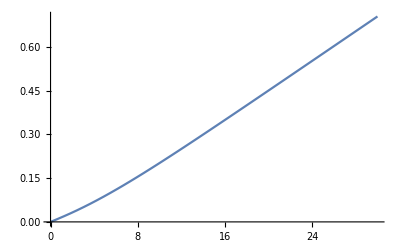

```mathematica
Plot[fcorr[αa,βa,v0a,αb,βb,v0b,mνa,mνb,σνa,σνb,λ1a,λ1b,μ1a,μ1b,ρab11,ρba12,ρab12,τ]/.{
v0a-> param2[[81,2]], αa-> param2[[82,2]],βa-> param2[[84,2]],σa-> param2[[86,2]],v0b-> param2[[121,2]], αb-> param2[[122,2]],βb-> param2[[124,2]],σb-> param2[[126,2]],ρbb12-> param2[[153,9]],ρaa12->param2[[150,6]] ,ρab11->param2[[151,6]],ρab12-> param2[[153,6]],ρba12-> param2[[151,8]],ρab22-> param2[[153,8]],μ1a-> param2[[68,2]],μ1b->param2[[108,2]],λ1a->param2[[70,2]] ,λ1b->param2[[110,2]],mνa->param2[[73,2]],σνa->param2[[75,2]],mνb->param2[[113,2]],σνb->param2[[115,2]],t-> 30.0},{τ,0,30}]
```

```mathematica
fcorr[αa,βa,v0a,αb,βb,v0b,mνa,mνb,σνa,σνb,λ1a,λ1b,μ1a,μ1b,ρab11,ρba12,ρab12,30]/.{
v0a-> param2[[81,2]],αa-> param2[[82,2]], βa-> param2[[84,2]],σa-> param2[[86,2]],v0b-> param2[[121,2]], αb-> param2[[122,2]],βb-> param2[[124,2]],σb-> param2[[126,2]],ρbb12-> param2[[153,9]],ρaa12->param2[[150,6]] ,ρab11->param2[[151,6]],ρab12-> param2[[153,6]],ρba12-> param2[[151,8]],ρab22-> param2[[153,8]],μ1a-> param2[[68,2]],μ1b->param2[[108,2]],λ1a->param2[[70,2]] ,λ1b->param2[[110,2]],mνa->param2[[73,2]],σνa->param2[[75,2]],mνb->param2[[113,2]],σνb->param2[[115,2]],t-> 30.0}
```

0.856717

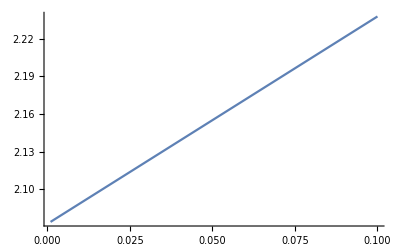

```mathematica
Plot[fcorr[αa,βa,v0a,αb,βb,v0b,mνa,mνb,σνa,σνb,λ1a,λ1b,μ1a,μ1b,ρab11,ρba12,ρab12,30]/.{
v0a-> param2[[81,2]],αa-> param2[[82,2]],βa-> param2[[84,2]], σa-> param2[[86,2]],v0b-> param2[[121,2]], αb-> param2[[122,2]],βb-> param2[[124,2]],σb-> param2[[126,2]],ρbb12-> param2[[153,9]],ρaa12->param2[[150,6]] ,ρab11->param2[[151,6]],ρab12-> param2[[153,6]],ρba12-> param2[[151,8]],ρab22-> param2[[153,8]],μ1a-> param2[[68,2]],μ1b->param2[[108,2]],λ1a->param2[[70,2]] ,λ1b->param2[[110,2]],mνa->param2[[73,2]],σνa->param2[[75,2]],mνb->param2[[113,2]],σνb->param2[[115,2]],t-> 30.0},{μ1a,0.001,.1}]
```

```mathematica
βa-> param2[[84,2]],
```